# ch1Introduction.nb Some basic principles

## Test Cases

### testCase0017: (1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

#### Expansion at the origin

```mathematica
$theFunction=(1+4 z^2)+(5/2+3/4 z)w^2+(z-3/4 z^2)w^3


aForm[$theFunction]
aForm[$theFunction]//TeXForm
```

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

\left(1+4 z^2\right)+\left(\frac{5}{2}+\frac{3}{4} z\right) w^2+\left(z-\frac{3}{4} z^2\right) w^3

### Checking f_w(s_i,w_i)=0 for each singular point and some w_i with f(s_i,w_i)=0

```mathematica
res= Resultant[$theFunction,D[$theFunction,w],w];
singList=DeleteDuplicates@NSolveValues[res==0,z];
wVals=NSolveValues[$theFunction==0/.z->singList[[2]],w]
D[$theFunction,w]/.{z->singList[[2]],w->#}&/@ wVals
```

{-0.406393-0.724149 ⅈ,0.812786+1.4483 ⅈ,0.812786+1.4483 ⅈ}

{-1.95584-5.02162 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ}

### testCase0023:

#### Expansion at the origin

```mathematica
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 



aForm[$theFunction]
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

### Checking f_w(s_i,w_i)=0 for each singular point and some w_i with f(s_i,w_i)=0

```mathematica
res= Resultant[$theFunction,D[$theFunction,w],w];
singList=DeleteDuplicates@NSolveValues[res==0,z];
wVals=NSolveValues[$theFunction==0/.z->singList[[2]],w]
D[$theFunction,w]/.{z->singList[[2]],w->#}&/@ wVals
```

{-0.406393-0.724149 ⅈ,0.812786+1.4483 ⅈ,0.812786+1.4483 ⅈ}

{-1.95584-5.02162 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ}

### testCase0032: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;


aForm[$theFunction]
aForm[$theFunction]//TeXForm
```

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

\left(-z^2+1 z^3\right)+\left(-4 z+3 z^2\right) w+\left(-z^3-9 z^4\right) w^2+\left(-2+8 z+4 z^2-4 z^3\right) w^3+\left(6-8
   z^2+7 z^3+8 z^4\right) w^4

### Checking f_w(s_i,w_i)=0 for each singular point and some w_i with f(s_i,w_i)=0

```mathematica
res= Resultant[$theFunction,D[$theFunction,w],w];
singList=DeleteDuplicates@NSolveValues[res==0,z];
wVals=NSolveValues[$theFunction==0/.z->singList[[2]],w]
D[$theFunction,w]/.{z->singList[[2]],w->#}&/@ wVals
```

{-0.406393-0.724149 ⅈ,0.812786+1.4483 ⅈ,0.812786+1.4483 ⅈ}

{-1.95584-5.02162 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ}

## Checking f_w(s_i,w_i)=0 for each singular point and some w_i with f(s_i,w_i)=0

```mathematica
res= Resultant[$theFunction,D[$theFunction,w],w];
singList=DeleteDuplicates@NSolveValues[res==0,z];
wVals=NSolveValues[$theFunction==0/.z->singList[[2]],w]
D[$theFunction,w]/.{z->singList[[2]],w->#}&/@ wVals
```

{-0.406393-0.724149 ⅈ,0.812786+1.4483 ⅈ,0.812786+1.4483 ⅈ}

{-1.95584-5.02162 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ}

## Illustrate z^{1/2}

### Use built-in z^{1/2} function

#### Illustrate imaginary sheets

```mathematica
imag1= ParametricPlot3D[{Re@z,Im@z,Im[z^{1/2}]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Blue}];
imag2= ParametricPlot3D[{Re@z,Im@z,-Im[z^{1/2}]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Red}];
Show[{imag1,imag2},PlotRange->All,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]
```

-Graphics3D-

Notice in the following code how a contour over the default definition of z^{1/2} starting at z=1 on the blue sheet and encounters the default branch-cut at the negative real axis and abruptly drops down to the lower blue sheet of the branch rather than analyticallly-continuing onto the red sheet.

```mathematica
imagContour=ParametricPlot3D[{Re@z,Im@z,Im[z^(1/2)]}/.z->Exp[I t],{t,0,2 Pi},PlotStyle->Yellow];
Show[{imag1,imag2,imagContour},PlotRange->All,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]
```

-Graphics3D-

#### Illustrate real sheets

```mathematica
real1= ParametricPlot3D[{Re@z,Im@z,Re[z^{1/2}]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Blue}];
real2= ParametricPlot3D[{Re@z,Im@z,-Re[z^{1/2}]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Red}];
Show[{real1,real2},PlotRange->All,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]
```

-Graphics3D-

The same branch-cut discontinuity is observed over the real sheets

```mathematica
realContour=ParametricPlot3D[{Re@z,Im@z,Re[z^(1/2)]}/.z->Exp[I t],{t,0,2 Pi},PlotStyle->Yellow];
Show[{real1,real2,realContour},PlotRange->All,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]
```

-Graphics3D-

#### Illustrate contour over z^{1/2} using default definition of z^{1/2} encounters branch-cut

```mathematica
contour1=ParametricPlot3D[{Re@z,Im@z,Im[z^(1/2)]}/.z->Exp[I t],{t,0,2 Pi},PlotStyle->Yellow];
Show[{b1,b2,contour1},PlotRange->All,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]
```

-Graphics3D-

### Use exponential form of z^{1/2}: The same branch-cut discontinuity is observed in the exponential form

```mathematica
squareRoot[z_,k_]:=Abs[z]^(1/2) Exp[I/2(Arg[z]+2 k Pi)];
sReal1=ParametricPlot3D[{Re@z,Im@z,Im[squareRoot[z,0]]}/. z->r Exp[I t],{r,0.001,1},{t,-Pi,Pi},PlotRange->All,PlotStyle->{Opacity[0.25],Red}];
(*Plot sheet 2*)
sReal2=ParametricPlot3D[{Re@z,Im@z,Im[squareRoot[z,1]]}/. z->r Exp[I t],{r,0.001,1},{t,-Pi,Pi},PlotRange->All,PlotStyle->{Opacity[0.25],Blue}];
(*Show plots*)
Show[{sReal1,sReal2},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]
```

-Graphics3D-

### Create mIVP of z^{1/2} and contour over f(z,w)=-z+w^2 to illustrate analytically-continuous route over branch sheets

```mathematica
theFunction=-z+w^2;
(*
 start the contour at (1/2 Sqrt[1/2])
*)
z0=3/2;
w0=Sqrt[z0];
(*
 revolve around the branch sheets 4 Pi
*)
tStart=0;
tEnd=4 Pi;
(*
 create z(t)
*)
Z[t_]:=3/2 Exp[I t];
(*
 solve IVP
*)
wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) D[Z[t],t])/. {w->w[t],z->Z[t]});
theSol=NDSolveValue[{wDeriv,w[tStart]==w0},w,{t,tStart,tEnd}];

mPlot=ParametricPlot3D[{Re@z,Im@z,Re@theSol[t]}/. z->Z[t],{t,tStart,tEnd},PlotStyle->{Thickness[0.01],Black}];

Show[{real1,real2,mPlot},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Re(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],PlotRange->All,BoxRatios->{1, 1, 1}]
```

-Graphics3D-

### Interactive 3D plot of mIVP contour analytically-continuing across branch surfaces

```mathematica
gPoint3D=Graphics3D@{PointSize[0.02],Green,Point@{Re@Z[tStart],Im@Z[tStart],Re@theSol[tStart]}};
 Manipulate[
ppReal=ParametricPlot3D[{Re@z,Im@z,Re@theSol[t]}/. z->Z[t],{t,tStart,tStop},PlotStyle->{Thickness[0.01],Black}];
arrowArray=Table[{Re@z,Im@z,Re@theSol[t]}/.z->Z[t],{t,tStart+0.1,tStop,(tStop-tStart)/50}];
arrowG=Graphics3D@{Thickness[0.005],Arrow@arrowArray};
Show[{real1,real2,arrowG,gPoint3D},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["Re[z]",14,Bold,Black],Style["Im[z]",14,Bold,Black],Style["Re(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],PlotRange->All],
{{tStop,tStart+0.001},tStart+0.001,tEnd}


]
```

ParametricPlot3D::plln: Limiting value tStart in {t,tStart,12.5664} is not a machine-sized real number.

Table::iterb: Iterator {t,0.1+tStart,12.5664,1/50 (12.5664-tStart)} does not have appropriate bounds.

Show::gcomb: Could not combine the graphics objects in Show[{real1,real2,,gPoint3D},AxesEdge→{{-1,-1},{1,-1},{-1,-1}},FaceGrids→{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel→{Re[z],Im[z],Re(w)},FaceGridsStyle→Directive[color,Dashing[{0,Small}]],PlotRange→All].

ParametricPlot3D::plln: Limiting value tStart in {t,tStart,12.5664} is not a machine-sized real number.

Table::iterb: Iterator {t,0.1+tStart,12.5664,1/50 (12.5664-tStart)} does not have appropriate bounds.

Show::gcomb: Could not combine the graphics objects in Show[{real1,real2,,gPoint3D},AxesEdge→{{-1,-1},{1,-1},{-1,-1}},FaceGrids→{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel→{Re[z],Im[z],Re(w)},FaceGridsStyle→Directive[color,Dashing[{0,Small}]],PlotRange→All].

## Study of testCase0032

```mathematica
function0032=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;

pSeries=w/.AsymptoticSolve[function0032==0,w,{z,0,5}]//N
```

{-0.25 z+0.0703125 z^2+0.020752 z^3+0.0039978 z^4-0.106094 z^5,(0.-1.41421 ⅈ) √z-2.875 z+(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2-(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3+(0.+38916.8 ⅈ) z^(7/2)+329091. z^4-(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5,(0.+1.41421 ⅈ) √z-2.875 z-(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2+(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3-(0.+38916.8 ⅈ) z^(7/2)+329091. z^4+(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5,0.333333+4.66667 z-168.222 z^2+9523.5 z^3-658181. z^4+5.05604×10^7 z^5}

### Compute $theSingularList

```mathematica
theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->workingPrecision],Abs@#1<= Abs@#2&];
res=Resultant[function0032,D[function0032,w],w]
theSingularSet=Sort[NSolveValues[res==0,z,WorkingPrecision->50],Abs@#1<= Abs@#2&];
theSingularSet//N
setPrec=Precision@theSingularSet
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(setPrec-10)&];
theSingularList//N
```

### Manually conjugate pSeries[[2]]

```mathematica
$reim=Re;
theSeries=pSeries[[2]];
expList=Exponent[theSeries,z,List]
coefList=Coefficient[theSeries,z,#]&/@ expList
p2Conj=Plus@@MapThread[#1 z^#2 Exp[2 Pi I #2]&,{coefList,expList}]
{theSeries//N,p2Conj//N}//MatrixForm
pSeries[[2;;3]]//MatrixForm
```

{1/2,1,3/2,2,5/2,3,7/2,4,9/2,5}

{0.-1.41421 ⅈ,-2.875,0.+13.3301 ⅈ,83.9648,0.-611.292 ⅈ,-4762.51,0.+38916.8 ⅈ,329091.,0.-2.85553×10^6 ⅈ,-2.52802×10^7}

(0.+1.41421 ⅈ) √z-2.875 z-(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2+(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3-(0.+38916.8 ⅈ) z^(7/2)+329091. z^4+(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5

((0.-1.41421 ⅈ) √z-2.875 z+(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2-(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3+(0.+38916.8 ⅈ) z^(7/2)+329091. z^4-(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5
(0.+1.41421 ⅈ) √z-2.875 z-(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2+(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3-(0.+38916.8 ⅈ) z^(7/2)+329091. z^4+(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5)

### Generate 50 terms of testCase0032 at origin and plot branch sheets

```mathematica
pSeries=w/.AsymptoticSolve[function0032==0,w,{z,0,50}]//N
```

```mathematica
f321=ParametricPlot3D[{Re@z,Im@z,Im@pSeries[[2]]}/.z->r Exp[I t],{r,0,1/1000},{t,-Pi,Pi},PlotRange->All,BoxRatios->{1, 1, 1}];
f322=ParametricPlot3D[{Re@z,Im@z,Im@pSeries[[3]]}/.z->r Exp[I t],{r,0,1/1000},{t,-Pi,Pi},PlotRange->All,BoxRatios->{1, 1, 1}];
Show[{f321,f322},PlotRange->All]
```

-Graphics3D-

## Study of testCase0023 using AsymptoticSolve

```mathematica
theConst=2/3+ⅈ/4;
function0023=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4;
```

### Compute series to order 50 (200 terms for 4-cycle)

```mathematica
pSeries=w/.AsymptoticSolve[function0023==0,w,{z,0,50}];
pSeries[[All,1;;5]]//N//MatrixForm
```

((-0.666667-0.25 ⅈ)-(0.2799+0.244276 ⅈ) z^(1/4)+(0.0176408+0.032719 ⅈ) √z+(0.012384+0.0906903 ⅈ) z^(3/4)+(0.00770177-0.0339537 ⅈ) z
(-0.666667-0.25 ⅈ)-(0.244276-0.2799 ⅈ) z^(1/4)-(0.0176408+0.032719 ⅈ) √z-(0.0906903-0.012384 ⅈ) z^(3/4)+(0.00770177-0.0339537 ⅈ) z
(-0.666667-0.25 ⅈ)+(0.244276-0.2799 ⅈ) z^(1/4)-(0.0176408+0.032719 ⅈ) √z+(0.0906903-0.012384 ⅈ) z^(3/4)+(0.00770177-0.0339537 ⅈ) z
(-0.666667-0.25 ⅈ)+(0.2799+0.244276 ⅈ) z^(1/4)+(0.0176408+0.032719 ⅈ) √z-(0.012384+0.0906903 ⅈ) z^(3/4)+(0.00770177-0.0339537 ⅈ) z
(0.666667+0.25 ⅈ)-(0.2799+0.244276 ⅈ) z^(1/4)-(0.0176408+0.032719 ⅈ) √z+(0.012384+0.0906903 ⅈ) z^(3/4)-(0.00770177-0.0339537 ⅈ) z
(0.666667+0.25 ⅈ)-(0.244276-0.2799 ⅈ) z^(1/4)+(0.0176408+0.032719 ⅈ) √z-(0.0906903-0.012384 ⅈ) z^(3/4)-(0.00770177-0.0339537 ⅈ) z
(0.666667+0.25 ⅈ)+(0.244276-0.2799 ⅈ) z^(1/4)+(0.0176408+0.032719 ⅈ) √z+(0.0906903-0.012384 ⅈ) z^(3/4)-(0.00770177-0.0339537 ⅈ) z
(0.666667+0.25 ⅈ)+(0.2799+0.244276 ⅈ) z^(1/4)-(0.0176408+0.032719 ⅈ) √z-(0.012384+0.0906903 ⅈ) z^(3/4)-(0.00770177-0.0339537 ⅈ) z
-1.9726/z^(1/4)-(0.5598+0.488553 ⅈ) z^(1/4)+(0.0247681+0.181381 ⅈ) z^(3/4)+(0.0426432-0.0648286 ⅈ) z^(5/4)-(0.0324034-0.00901773 ⅈ) z^(7/4)
(0.+1.9726 ⅈ)/z^(1/4)+(0.488553-0.5598 ⅈ) z^(1/4)+(0.181381-0.0247681 ⅈ) z^(3/4)+(0.0648286+0.0426432 ⅈ) z^(5/4)+(0.00901773+0.0324034 ⅈ) z^(7/4)
-(0.+1.9726 ⅈ)/z^(1/4)-(0.488553-0.5598 ⅈ) z^(1/4)-(0.181381-0.0247681 ⅈ) z^(3/4)-(0.0648286+0.0426432 ⅈ) z^(5/4)-(0.00901773+0.0324034 ⅈ) z^(7/4)
1.9726/z^(1/4)+(0.5598+0.488553 ⅈ) z^(1/4)-(0.0247681+0.181381 ⅈ) z^(3/4)-(0.0426432-0.0648286 ⅈ) z^(5/4)+(0.0324034-0.00901773 ⅈ) z^(7/4))

### Set up Approximate Root Test

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200}

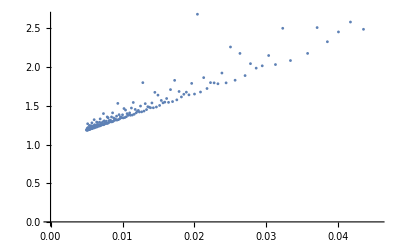

```mathematica
expList=Exponent[pSeries[[1]],z,List];
coefList=Coefficient[pSeries[[1]],z,#]&/@ expList;
theLCM=LCM@@(Denominator@expList);
 numerators=theLCM expList
rootTestTable=Table[
{1/numerators[[k]],N[1/(Abs[coefList[[k]]]^(4/numerators[[k]])),25]},
{k,15,Length@coefList}];
lp1=ListPlot[rootTestTable,PlotStyle->{PointSize[0.005]},AxesOrigin->{0,0}]
```

## Initialization

### aForm

```mathematica
(*evaluate the symbol to force autoloading*)Convert`TeX`ExpressionToTeX;

(*modify ExpressionToTeX so that it blocks $TeX to true*)
Unprotect[Convert`TeX`ExpressionToTeX];
Convert`TeX`ExpressionToTeX[expr_,o___?OptionQ]/;!TrueQ@$TeX:=Block[{$TeX=True},Convert`TeX`ExpressionToTeX[expr,o]]
Protect[Convert`TeX`ExpressionToTeX];

(*modify ordplus to reverse the order of polynomials*)
TraditionalFormDump`ordplus[x_,y_]/;$TeX:=Block[{$TeX=False},Reverse@TraditionalFormDump`ordplus[x,y]]

(*introduce the wrapper function ParameterVariableForm to allow one to specify what the*parameter variable is,that is,what variables are not the main polynomial variable*)
Options[ParameterVariableForm]={ParameterVariables->{}};

Unprotect[Times];
Times/:MakeBoxes[r_Rational s_,TraditionalForm]/;$TeX:=RowBox[{MakeBoxes[r,TraditionalForm],MakeBoxes[s,TraditionalForm]}]
Protect[Times];

ParameterVariableForm/:MakeBoxes[ParameterVariableForm[x_,opts:OptionsPattern[]],TraditionalForm]:=MakeBoxes[TraditionalForm[x,opts],TraditionalForm]

(*helper functions*)ClearAll[thecRules,toPowerBoxes,parenthesizeRow,coeffToBoxes,toMonomialBoxes];
thecRules[t_][poly_]:=Association@Sort@CoefficientRules[poly,{t}];
toPowerBoxes[t_]:=KeyMap[MakeBoxes[#]&[t^#]&@*First];
parenthesizeRow[boxes:{b:Except[_List]}]:=RowBox[{"(",b,")"}];
parenthesizeRow[boxes_]:=RowBox[{"(",RowBox@Flatten@boxes,")"}];coeffToBoxes//ClearAll;
(*first coeff is treated different*)
coeffToBoxes[assoc_]:=MapAt[MakeBoxes,1]@MapAt[{If[Negative[#],"-","+"],MakeBoxes[#]&@Abs@#}&,2;;]@assoc;
(*±1 are specials cases;no zero coeffs*)
toMonomialBoxes["1",coeff_]:=coeff;
toMonomialBoxes[power_,{sign_,coeff_}]:={sign,RowBox[{coeff," ",power}]};
toMonomialBoxes[power_,"1"]:=power;
toMonomialBoxes[power_,RowBox[{"-","1"}]]:=RowBox[{"-",power}];
toMonomialBoxes[power_,coeff_]:=RowBox[{coeff," ",power}];

aForm[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[z]@*thecRules[z]]@toPowerBoxes[w]@thecRules[w][f];

aForm2[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[c]@*thecRules[c]]@toPowerBoxes[z]@thecRules[z][f];
```